### Distribution of electrons in certain energy levels for {n_i}

```mathematica
distributeelectrons[ne_,nstates_]:=Module[{},Permutations[Join[Table[0,{i,1,nstates-ne}],Table[1,{i,1,ne}]]]]
```

```mathematica
distributeelectrons[2,5]
```

{{0,0,0,1,1},{0,0,1,0,1},{0,0,1,1,0},{0,1,0,0,1},{0,1,0,1,0},{0,1,1,0,0},{1,0,0,0,1},{1,0,0,1,0},{1,0,1,0,0},{1,1,0,0,0}}

```mathematica
distributeelectrons[1,2]

Print[hello]
```

{{0,1},{1,0}}

hello

### Define energy levels for {E_i}

```mathematica
enlist=Table[0,{i,0,1}]
```

{0,0}

### Free energy

```mathematica
freee[kt_,ne_,elist_]:=Module[{nstates,dislist,fe},nstates=Length[elist];dislist=distributeelectrons[ne,nstates];fe=-kt*Log[Sum[Exp[-1/kt*Sum[elist[[j]]*dislist[[i,j]],{j,1,nstates}]],{i,1,Length[dislist]}]];Return[fe]]
```

```mathematica
freee[10.,0,enlist]
```

freee[10.,0,{0,0}]

```mathematica
10*Log[2.]
```

6.93147

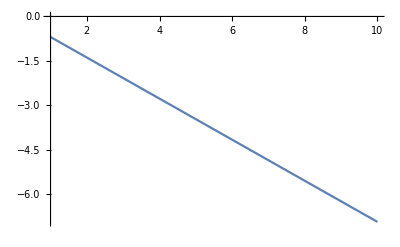

```mathematica
Plot[freee[mykt,1,enlist],{mykt,1,10}]
```

```mathematica
enlist=Table[i,{i,0,1}]
```

{0,1}

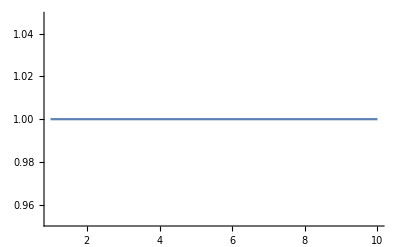

```mathematica
Plot[freee[mykt,2,enlist],{mykt,1,10}]
```

### Charging energy

1/2

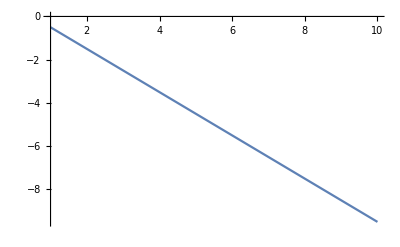

```mathematica
U[C_,ne_,qext_] := ((((ne)-qext)^2)/(2*C)) - (((qext)^2)/(2*C))
U[1,1,0]


Plot[U[1, 1, qext],{qext, 1,10}]
```

### Thermodynamic potential

-1/2-10 Log[2]

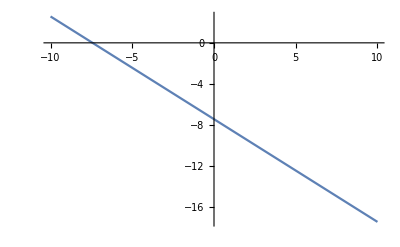

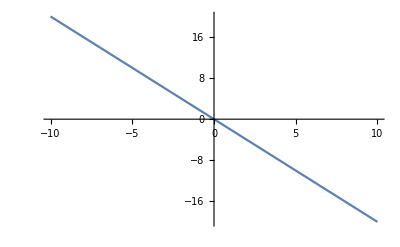

Show::gcomb: Could not combine the graphics objects in Show[%124,%125].

Show[%124,%125]

```mathematica
Ω[C_,ne_,kt_,ef_,qext_,enlist_] := Module[{},Return[freee[kt,ne,enlist] + U[C,ne,qext] - ne*ef]]
Ω[1, 1, 10, 1, 0, enlist]

Plot[Ω[1,1, 10, 1, qext, enlist], {qext, -10,10}]

Plot[Ω[1,2, 10, 1, qext, enlist], {qext, -10,10}]

Show[%124, %125]
```

### Equilibrium distributions

```mathematica
enlist
```

{0,0,0}

```mathematica
peq[C_,ne_,kt_,ef_,qext_,enlist_]:=Module[{nne,psum,ne2},ne2=Length[enlist];psum=Sum[Exp[-Ω[C,nne,kt,ef,qext,enlist] /kt],{nne,0,ne2}];Return[Exp[-Ω[C,ne,kt,ef,qext,enlist] /kt]/psum]]
peq[1,1,10,1,2,enlist]

enlist
```

ⅇ^(1/10 (5/2+10 Log[2]))/(1+ⅇ^(2/5)+ⅇ^(1/10 (5/2+10 Log[2])))

{0,0}

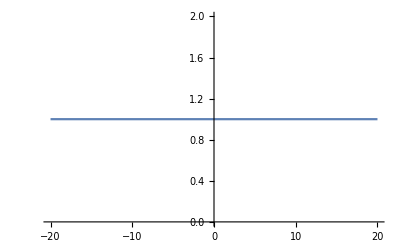

```mathematica
Plot[Sum[peq[1,jj,1,qext,1,enlist],{jj,0,3,1}], {qext, -20,20},PlotRange->All]
```

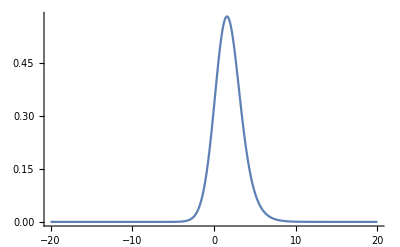

```mathematica
Plot[peq[1,2,1,qext,1,enlist], {qext, -20,20},PlotRange->All]
```

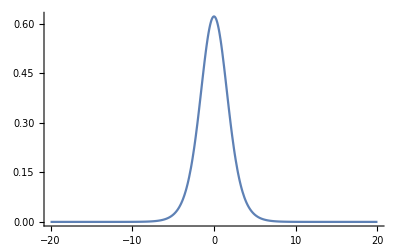

```mathematica
Plot[peq[1,1,1,qext,1,enlist], {qext, -20,20},PlotRange->All]
```

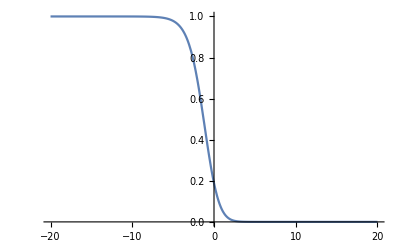

```mathematica
Plot[peq[1,0,1,qext,1,enlist], {qext, -20,20}]
```

```mathematica
feq[p_,ne_,kt_,elist_]:=Module[{nstates,dislist,psum},nstates=Length[elist];dislist=distributeelectrons[ne,nstates];psum=Sum[Exp[-1/kt*Sum[elist[[j]]*dislist[[i,j]],{j,1,nstates}]]*KroneckerDelta[dislist[[i,p]],1],{i,1,Length[dislist]}];Return[psum*(Exp[freee[kt,ne,elist]/kt])]]
```

```mathematica
feq[1,1,0.5,{0,1.}]
```

0.880797

```mathematica
feq[1,0,10,enlist]
```

0

```mathematica
feq[1,1,10,enlist]
```

1/2

### Fermi distribution function

```mathematica
F[kt_,E_] := (1+ Exp[(E)/(kt)])^(-1)
```

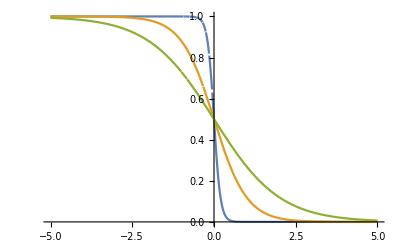

```mathematica
Plot[{F[0.1,E],F[0.5,E], F[1,E]},{E, -5, 5}]
```

### Conductivity

```mathematica
enlist
```

{0,0}

```mathematica
gf[gammapl_,gammapr_,C_,kt_,elist_,ef_,qext_]:=Module[{nstates},nstates=Length[elist];Return[1/kt*Sum[(gammapl*gammapr)/(gammapl+gammapr)*peq[C,ne,kt,ef,qext,elist]*feq[p,ne,kt,elist]*(1-F[kt,elist[[p]]+U[C,ne,qext]-U[C,ne-1,qext]-ef]),{p,1,nstates},{ne,1,nstates}]]]
```

```mathematica
?peq
```

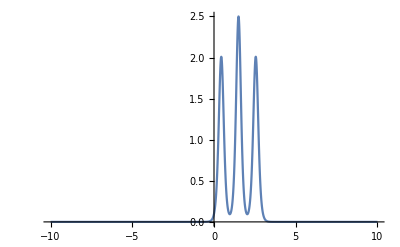

```mathematica
Plot[gf[1.,1.,1.,0.1,{0,0,0},0.,qext],{qext, -10, 10}, PlotRange-> All]
```

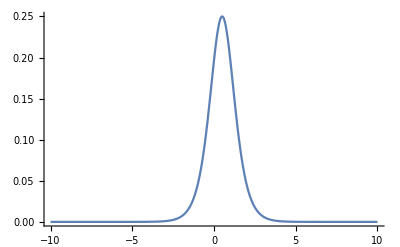

```mathematica
Plot[gf[1.,1.,1.,0.5,{0},0.,qext],{qext, -10, 10}, PlotRange-> All]
```

0.0249838

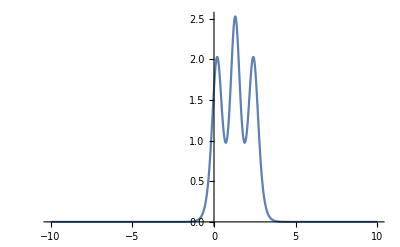

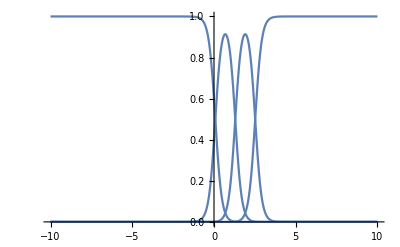

```mathematica
gf[1.,1.,1.,10.,enlist,0.1,1.0]

Plot[gf[1.,1.,2.,0.1,{0,0, 0},0.1,qext],{qext, -10, 10}, PlotRange-> All]
Plot[  Table[ peq[2.,ne,0.1,0.1,qext,{0,0, 0}],{ne,0,3}],{qext, -10,10}]
```

```mathematica
efl[C_,ne_,qext_, eta_, eV_, ep_] :=ep+ U[C,ne,qext] - U[C,(ne-1),qext] + (eta)*(eV)

eil[C_,ne_,qext_, eta_, eV_, ep_] :=ep+ U[C,(ne+1),qext] - U[C,ne,qext] + (eta)*(eV)

efr[C_,ne_,qext_, eta_, eV_, ep_] :=ep+ U[C,ne,qext] - U[C,(ne-1),qext] - (1-eta)*(eV)

eir[C_,ne_,qext_, eta_, eV_, ep_] :=ep+ U[C,(ne+1),qext] - U[C,ne,qext] - (1-eta)*(eV)
```

```mathematica
efl[1,0,0,0,0,0]
U[1,-1,0]
```

-1/2

1/2

#### Probability Solution

```mathematica
Solve[pout*((1- F[0.1, efl[1,(1+1),5,1,0.1]])+(1-F[0.1, efr[1,(1+1),5,1,0.1]]))== (1-pout)* ( F[0.1, eil[1,1,5,1,0.1]]+(F[0.1, eir[1,1,5,1,0.1]])),pout]
```

{{pout→1/2 (F[0.1,-3.5]+F[0.1,-3.4])}}

### Stationary current

```mathematica
Istat[gammapl_, P_,C_,ne_,qext_, eta_, eV_, kt_, ef_, elist_] := Module[{nstates,dislist,output},nstates=Length[elist];dislist=distributeelectrons[ne,nstates];output=-Sum[Sum[gammapl*P*((KroneckerDelta[dislist[[i,p]],0])*F[kt,(eil[C,ne, qext, eta, eV ]-ef)]-(KroneckerDelta[dislist[[i,p]],1])*(1-F[kt,(efl[C,ne, qext, eta, eV ]-ef)])),{i,1,Length[dislist]}],{p,1,nstates}];
Return[output]]

Istat[1,0.5, 1, 1, 5, 1, 0.1, 0.1, 0, enlist]
```

-1./(1+ⅇ^(10. eil[1,1,5,1,0.1]))-1. (-1+1/(1+ⅇ^(10. efl[1,1,5,1,0.1])))

```mathematica
numerator[gammapl_, gammapr_, C_,ne_,qext_, eta_, eV_ , kt_,ep_, ef_] := gammapl*( F[kt, eil[C,ne,qext, eta, eV, ep]- ef])+ gammapr*(F[kt, eir[C,ne,qext, eta, eV, ep]-ef])
```

```mathematica
denominator[gammapl_, gammapr_, C_,ne_,qext_, eta_, eV_ , kt_, ep_, ef_] := gammapl* (1-F[kt, efl[C,(ne+1),qext, eta, eV, ep]-ef]) + gammapr*(1-F[kt, efr[C,(ne+1),qext, eta, eV, ep]-ef])
```

```mathematica
numerator[1,1,1,0,0,0,0, 1,0,1]
eil[1,0,0,0,0,0]
denominator[1,1,1,0,0,0,0, 1,0,1]
```

2/(1+1/(√ⅇ))

1/2

2-2/(1+1/(√ⅇ))

```mathematica
ratio[gammapl_, gammapr_, C_,ne_,qext_, eta_, eV_ , kt_,ep_, ef_] := numerator[gammapl, gammapr, C,ne,qext, eta, eV , kt, ep,ef]/ denominator[gammapl, gammapr, C,ne,qext, eta, eV , kt, ep, ef]
```

```mathematica
a[1]=1/(ratio[1,1,1,0,5,0.5,0.1, 1,0,0])
```

0.0111226

```mathematica
a[2] =1/( ratio[1,1,1,1,5,0.5,0.1, 1,0,0])
```

0.0302329

```mathematica
a[3]=ratio[1,1,1,1,5,0.5,0.1, 1,0,0]
```

33.0765

```mathematica
product[1] = a[1]*a[2]*a[3]
```

0.0111226

```mathematica
product[2] = a[2]*a[3]
```

1.

```mathematica
P[4] = 1/(1+product[1]+product[2]+a[3])
```

0.0285001

```mathematica
P[3] = P[4]*a[3]
```

0.942683

```mathematica
P[2] = a[2]*P[3]
```

0.0000260499

```mathematica
P[1] = a[1]*P[2]
```

2.89742×10^-7

```mathematica
P[1]+P[2]+P[3]+P[4]
```

0.029388

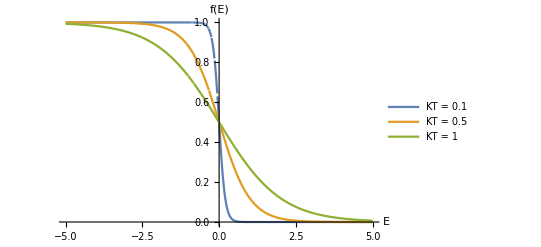

```mathematica
graph = Plot[{F[0.1,E],F[0.5,E], F[1,E]},{E, -5, 5}, AxesLabel->{"E","f(E)"}, PlotLegends -> {"KT = 0.1", "KT = 0.5","KT = 1" }]
```

```mathematica
Export["Fermi_distribution_functions.png",graph]
```

Fermi_distribution_functions.png

```mathematica
Findladder[n_] := 
Module[{w,x,y, z},
w = Findladder[n-1];
x = Reverse[w];
y = Transpose[Join[ {Table[0,{i,1,2^(n-1)}]},Transpose[w]]];
z = Transpose[Join[ {Table[1,{i,1,2^(n-1)}]},Transpose[x]]];
Export["graycode."<>ToString[n]<>".dat",Join[y,z]];
Return[Join[y,z]]
]
```

```mathematica
Findladder[2]
```

{{0,0},{0,1},{1,1},{1,0}}

$IterationLimit::itlim: Iteration limit of 4096 exceeded.

General::stop: Further output of Transpose::permspec will be suppressed during this calculation.

Join::heads: Heads List and Transpose at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop,$IterationLimit::itlim,$IterationLimit::itlim,Join::heads,«1»,Transpose::«8»,Transpose::permspec,Transpose::permspec,General::stop,$IterationLimit::itlim,Join::heads,General::stop}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

Transpose::permspec: Invalid permutation specification found at position 2 in RowBox[{"Transpose", "[", RowBox[{Hold[RowBox[{Hold[MakeBoxes[Join, StandardForm]], "[", RowBox[{Hold[MakeBoxes[{{}}, StandardForm]], ",", Hold[MakeBoxes[Transpose[Transpose[Join[{{}}, Transpose[Transpose[Join[<<2>>], Join[<<2>>]]]], Join[{{}}, Transpose[Transpose[Join[<<2>>], Join[<<2>>]]]]]], StandardForm]]}], "]"}]], ",", Hold[RowBox[{Hold[MakeBoxes[Join, StandardForm]], "[", RowBox[{Hold[MakeBoxes[{{}}, StandardForm]], ",", Hold[MakeBoxes[Transpose[Transpose[Join[{{}}, Transpose[Transpose[Join[<<2>>], Join[<<2>>]]]], Join[{{}}, Transpose[Transpose[Join[<<2>>], Join[<<2>>]]]]]], StandardForm]]}], "]"}]]}], "]"}].

Transpose::permspec: Invalid permutation specification found at position 2 in RowBox[{"Transpose", "[", RowBox[{RowBox[{"Join", "[", RowBox[{RowBox[{"{", RowBox[{"{", "}"}], "}"}], ",", RowBox[{"Transpose", "[", Hold[RowBox[{Hold[MakeBoxes[Transpose, StandardForm]], "[", RowBox[{Hold[MakeBoxes[Join[{{}}, Transpose[Transpose[Join[<<2>>], Join[<<2>>]]]], StandardForm]], ",", Hold[MakeBoxes[Join[{{}}, Transpose[Transpose[Join[<<2>>], Join[<<2>>]]]], StandardForm]]}], "]"}]], "]"}]}], "]"}], ",", RowBox[{"Join", "[", RowBox[{RowBox[{"{", RowBox[{"{", "}"}], "}"}], ",", RowBox[{"Transpose", "[", Hold[RowBox[{Hold[MakeBoxes[Transpose, StandardForm]], "[", RowBox[{Hold[MakeBoxes[Join[{{}}, Transpose[Transpose[Join[<<2>>], Join[<<2>>]]]], StandardForm]], ",", Hold[MakeBoxes[Join[{{}}, Transpose[Transpose[Join[<<2>>], Join[<<2>>]]]], StandardForm]]}], "]"}]], "]"}]}], "]"}]}], "]"}].

Join::heads: Heads List and Transpose at positions 1 and 2 are expected to be the same.

Transpose::permspec: Invalid permutation specification found at position 2 in RowBox[{"Transpose", "[", RowBox[{RowBox[{"Join", "[", RowBox[{RowBox[{"{", RowBox[{"{", "}"}], "}"}], ",", RowBox[{"Transpose", "[", Hold[RowBox[{Hold[MakeBoxes[Transpose, StandardForm]], "[", RowBox[{Hold[MakeBoxes[Join[{{}}, Transpose[Transpose[Join[<<2>>], Join[<<2>>]]]], StandardForm]], ",", Hold[MakeBoxes[Join[{{}}, Transpose[Transpose[Join[<<2>>], Join[<<2>>]]]], StandardForm]]}], "]"}]], "]"}]}], "]"}], ",", RowBox[{"Join", "[", RowBox[{RowBox[{"{", RowBox[{"{", "}"}], "}"}], ",", RowBox[{"Transpose", "[", Hold[RowBox[{Hold[MakeBoxes[Transpose, StandardForm]], "[", RowBox[{Hold[MakeBoxes[Join[{{}}, Transpose[Transpose[Join[<<2>>], Join[<<2>>]]]], StandardForm]], ",", Hold[MakeBoxes[Join[{{}}, Transpose[Transpose[Join[<<2>>], Join[<<2>>]]]], StandardForm]]}], "]"}]], "]"}]}], "]"}]}], "]"}].

General::stop: Further output of Transpose::permspec will be suppressed during this calculation.

$IterationLimit::itlim: Iteration limit of 4096 exceeded.

Export::infer: Cannot infer format of file graycode.-500.dat.

Join::heads: Heads List and Transpose at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

$IterationLimit::itlim: Iteration limit of 4096 exceeded.

General::stop: Further output of $IterationLimit::itlim will be suppressed during this calculation.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop,Transpose::permspec,Transpose::permspec,Join::heads,«3»,$IterationLimit::itlim,Export::infer,$IterationLimit::itlim,Join::heads,General::stop,$IterationLimit::itlim,General::stop}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

```mathematica
occupation[n_] :=Module[{q, s,w, prototype},q = DeleteCases[Flatten[Table[ Table[If[Findladder[n][[i]][[j]]== Findladder[n][[i-1]][[j]], Findladder[n][[i]][[j]]],{j, 1,Length[Findladder[n][[i]]]}],{i,2,Length[Findladder[n]]}]], Null];
w = n-1;
s = Length[q]/w;
prototype = Table[q[[(w*(g-1))+1;;(w*g)]], {g,1,s}];
Return[Table[Total[prototype[[i]]],{i,1,Length[prototype]}]]

]
```

```mathematica
states[n_] :=DeleteCases[Flatten[Table[Table[If[Findladder[n][[i]][[j]]!= Findladder[n][[i-1]][[j]], j],{j, 1,Length[Findladder[n][[i]]]}],{i,2,Length[Findladder[n]]}]], Null]
```

```mathematica
s = Length[q]/2
```

7

```mathematica
w = Length[q]/s
```

2

```mathematica
prototype = Table[q[[(w*(g-1))+1;;(w*g)]], {g,1,s}]
q
```

{{0,0},{0,1},{0,1},{1,0},{1,1},{1,1},{1,0}}

{0,0,0,1,0,1,1,0,1,1,1,1,1,0}

```mathematica
{0,0,0,1,0,1,1,0,1,1,1,1,1,0}
```

{0,0,0,1,0,1,1,0,1,1,1,1,1,0}

```mathematica
Table[Total[prototype[[i]]],{i,1,Length[prototype]}]
```

{0,1,1,1,2,2,1,1,2,3,3,2,2,2,1}

{{2},{3},{1},{5}}

{{2,3},{2,1},{2,5},{2,4},{3,1},{3,5},{3,4},{1,5},{1,4},{5,4}}

```mathematica
ON[n_] := Table[{states[n][[i]],occupation[n][[i]]},{i,1,Length[states[n]]}]
```

{{2,0},{1,1},{2,1}}

{2,1,2}

{0,1,1}

```mathematica
AutoRatio[  gammapl_, gammapr_, C_,n_,qext_, eta_, eV_ , kt_,ep_, ef_] :=

Module[{number, con, stateslist} ,

 con = Findladder[n];
stateslist = states[n];
Return[

ParallelTable[1/(ratio[gammapl, gammapr, C,ON[n][[i]][[2]],qext, eta, eV, kt, ep[[stateslist[[i]]]], ef]^(power[n][[i]])),{i,1,(Length[ON[n]])}]

]
]
```

```mathematica
Print[hello]
```

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of w$7573=Findladder[-508-1];x$7573=Reverse[w$7573];y$7573=Transpose[Join[{Table[0,{i,1,Power[«2»]}]},Transpose[w$7573]]];z$7573=Transpose[Join[{Table[1,{i,1,Power[«2»]}]},Transpose[x$7573]]];Export[graycode.<>ToString[-508]<>.dat,Join[y$7573,z$7573]];Return[Join[y$7573,z$7573]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of 2^(-507-1).

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Hold[2^(-507-1)].

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

$IterationLimit::itlim: Iteration limit of 4096 exceeded.

Hold[Join::heads :  Heads List and Transpose at positions 1 and 2 are expected to be the same.]

Hold[Transpose::permspec :  Invalid permutation specification found at position 2 in Transpose[Join[{{}},Transpose[Hold[Return[Join[y$7572,z$7572]]]]],Join[{{}},Transpose[Hold[Return[Join[y$7572,z$7572]]]]]].]

Transpose::permspec: Invalid permutation specification found at position 2 in Transpose[Join[{{}},Transpose[Hold[Return[Join[y$7572,z$7572]]]]],Join[{{}},Transpose[Hold[Return[Join[y$7572,z$7572]]]]]].

$IterationLimit::itlim: Iteration limit of 4096 exceeded.

General::stop: Further output of Transpose::permspec will be suppressed during this calculation.

Join::heads: Heads List and Transpose at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop,$IterationLimit::itlim,$IterationLimit::itlim,Join::heads,«1»,Transpose::«8»,Transpose::permspec,Transpose::permspec,General::stop,$IterationLimit::itlim,Join::heads,General::stop}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

Transpose::permspec: Invalid permutation specification found at position 2 in RowBox[{"Transpose", "[", RowBox[{Hold[RowBox[{Hold[MakeBoxes[Join, StandardForm]], "[", RowBox[{Hold[MakeBoxes[{{}}, StandardForm]], ",", Hold[MakeBoxes[Transpose[Transpose[Join[{{}}, Transpose[Transpose[Join[<<2>>], Join[<<2>>]]]], Join[{{}}, Transpose[Transpose[Join[<<2>>], Join[<<2>>]]]]]], StandardForm]]}], "]"}]], ",", Hold[RowBox[{Hold[MakeBoxes[Join, StandardForm]], "[", RowBox[{Hold[MakeBoxes[{{}}, StandardForm]], ",", Hold[MakeBoxes[Transpose[Transpose[Join[{{}}, Transpose[Transpose[Join[<<2>>], Join[<<2>>]]]], Join[{{}}, Transpose[Transpose[Join[<<2>>], Join[<<2>>]]]]]], StandardForm]]}], "]"}]]}], "]"}].

Transpose::permspec: Invalid permutation specification found at position 2 in RowBox[{"Transpose", "[", RowBox[{RowBox[{"Join", "[", RowBox[{RowBox[{"{", RowBox[{"{", "}"}], "}"}], ",", RowBox[{"Transpose", "[", Hold[RowBox[{Hold[MakeBoxes[Transpose, StandardForm]], "[", RowBox[{Hold[MakeBoxes[Join[{{}}, Transpose[Transpose[Join[<<2>>], Join[<<2>>]]]], StandardForm]], ",", Hold[MakeBoxes[Join[{{}}, Transpose[Transpose[Join[<<2>>], Join[<<2>>]]]], StandardForm]]}], "]"}]], "]"}]}], "]"}], ",", RowBox[{"Join", "[", RowBox[{RowBox[{"{", RowBox[{"{", "}"}], "}"}], ",", RowBox[{"Transpose", "[", Hold[RowBox[{Hold[MakeBoxes[Transpose, StandardForm]], "[", RowBox[{Hold[MakeBoxes[Join[{{}}, Transpose[Transpose[Join[<<2>>], Join[<<2>>]]]], StandardForm]], ",", Hold[MakeBoxes[Join[{{}}, Transpose[Transpose[Join[<<2>>], Join[<<2>>]]]], StandardForm]]}], "]"}]], "]"}]}], "]"}]}], "]"}].

Join::heads: Heads List and Transpose at positions 1 and 2 are expected to be the same.

Transpose::permspec: Invalid permutation specification found at position 2 in RowBox[{"Transpose", "[", RowBox[{RowBox[{"Join", "[", RowBox[{RowBox[{"{", RowBox[{"{", "}"}], "}"}], ",", RowBox[{"Transpose", "[", Hold[RowBox[{Hold[MakeBoxes[Transpose, StandardForm]], "[", RowBox[{Hold[MakeBoxes[Join[{{}}, Transpose[Transpose[Join[<<2>>], Join[<<2>>]]]], StandardForm]], ",", Hold[MakeBoxes[Join[{{}}, Transpose[Transpose[Join[<<2>>], Join[<<2>>]]]], StandardForm]]}], "]"}]], "]"}]}], "]"}], ",", RowBox[{"Join", "[", RowBox[{RowBox[{"{", RowBox[{"{", "}"}], "}"}], ",", RowBox[{"Transpose", "[", Hold[RowBox[{Hold[MakeBoxes[Transpose, StandardForm]], "[", RowBox[{Hold[MakeBoxes[Join[{{}}, Transpose[Transpose[Join[<<2>>], Join[<<2>>]]]], StandardForm]], ",", Hold[MakeBoxes[Join[{{}}, Transpose[Transpose[Join[<<2>>], Join[<<2>>]]]], StandardForm]]}], "]"}]], "]"}]}], "]"}]}], "]"}].

General::stop: Further output of Transpose::permspec will be suppressed during this calculation.

$IterationLimit::itlim: Iteration limit of 4096 exceeded.

Export::infer: Cannot infer format of file graycode.-500.dat.

Join::heads: Heads List and Transpose at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

$IterationLimit::itlim: Iteration limit of 4096 exceeded.

General::stop: Further output of $IterationLimit::itlim will be suppressed during this calculation.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop,Transpose::permspec,Transpose::permspec,Join::heads,«3»,$IterationLimit::itlim,Export::infer,$IterationLimit::itlim,Join::heads,General::stop,$IterationLimit::itlim,General::stop}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

Transpose::permspec: Invalid permutation specification found at position 2 in Transpose[Join[{{}},Transpose[Transpose[Join[{{}},Transpose[Transpose[Join[2],Join[2]]]],Join[{{}},Transpose[Transpose[Join[2],Join[2]]]]]]],Join[{{}},Transpose[Transpose[Join[{{}},Transpose[Transpose[Join[2],Join[2]]]],Join[{{}},Transpose[Transpose[Join[2],Join[2]]]]]]]].

Transpose::permspec: Invalid permutation specification found at position 2 in Transpose[Join[{{}},Transpose[Transpose[Join[{{}},Transpose[Transpose[Join[«2»],Join[«2»]]]],Join[{{}},Transpose[Transpose[Join[«2»],Join[«2»]]]]]]],Join[{{}},Transpose[Transpose[Join[{{}},Transpose[Transpose[Join[«2»],Join[«2»]]]],Join[{{}},Transpose[Transpose[Join[«2»],Join[«2»]]]]]]]].

Join::heads: Heads List and Transpose at positions 1 and 2 are expected to be the same.

Transpose::permspec: Invalid permutation specification found at position 2 in Transpose[Join[{{}},Transpose[Transpose[Join[{{}},Transpose[Transpose[Join[«2»],Join[«2»]]]],Join[{{}},Transpose[Transpose[Join[«2»],Join[«2»]]]]]]],Join[{{}},Transpose[Transpose[Join[{{}},Transpose[Transpose[Join[«2»],Join[«2»]]]],Join[{{}},Transpose[Transpose[Join[«2»],Join[«2»]]]]]]]].

General::stop: Further output of Transpose::permspec will be suppressed during this calculation.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop,Transpose::permspec,Transpose::permspec,Join::heads,Join::heads,Transpose::permspec,General::stop}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

$IterationLimit::itlim: Iteration limit of 4096 exceeded.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop,$IterationLimit::itlim}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

Export::infer: Cannot infer format of file Hold[MakeBoxes["graycode.-497.dat", StandardForm]].

Transpose::permspec: Invalid permutation specification found at position 2 in Transpose[Join[{{}},Transpose[Transpose[Join[{{}},Transpose[Transpose[Join[«2»],Join[«2»]]]],Join[{{}},Transpose[Transpose[Join[«2»],Join[«2»]]]]]]],Join[{{}},Transpose[Transpose[Join[{{}},Transpose[Transpose[Join[«2»],Join[«2»]]]],Join[{{}},Transpose[Transpose[Join[«2»],Join[«2»]]]]]]]].

Join::heads: Heads List and Transpose at positions 1 and 2 are expected to be the same.

Transpose::permspec: Invalid permutation specification found at position 2 in Transpose[Join[{{}},Transpose[Transpose[Join[{{}},Transpose[Transpose[Join[«2»],Join[«2»]]]],Join[{{}},Transpose[Transpose[Join[«2»],Join[«2»]]]]]]],Join[{{}},Transpose[Transpose[Join[{{}},Transpose[Transpose[Join[«2»],Join[«2»]]]],Join[{{}},Transpose[Transpose[Join[«2»],Join[«2»]]]]]]]].

General::stop: Further output of Transpose::permspec will be suppressed during this calculation.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Message[Message::msgl,Hold[{$RecursionLimit::reclim2,$RecursionLimit::reclim2,$RecursionLimit::reclim2,General::stop,Export::infer,Transpose::permspec,Transpose::permspec,Join::heads,Join::heads,Transpose::permspec,General::stop}]].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {$RecursionLimit::reclim2}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ….

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

Export::infer: Cannot infer format of file graycode.-496.dat.

Transpose::permspec: Invalid permutation specification found at position 2 in Transpose[Join[{{}},Transpose[Transpose[Join[{{}},Transpose[Transpose[Join[«2»],Join[«2»]]]],Join[{{}},Transpose[Transpose[Join[«2»],Join[«2»]]]]]]],Join[{{}},Transpose[Transpose[Join[{{}},Transpose[Transpose[Join[«2»],Join[«2»]]]],Join[{{}},Transpose[Transpose[Join[«2»],Join[«2»]]]]]]]].

Join::heads: Heads List and Transpose at positions 1 and 2 are expected to be the same.

Transpose::permspec: Invalid permutation specification found at position 2 in Transpose[Join[{{}},Transpose[Transpose[Join[{{}},Transpose[Transpose[Join[«2»],Join[«2»]]]],Join[{{}},Transpose[Transpose[Join[«2»],Join[«2»]]]]]]],Join[{{}},Transpose[Transpose[Join[{{}},Transpose[Transpose[Join[«2»],Join[«2»]]]],Join[{{}},Transpose[Transpose[Join[«2»],Join[«2»]]]]]]]].

General::stop: Further output of Transpose::permspec will be suppressed during this calculation.

$IterationLimit::itlim: Iteration limit of 4096 exceeded.

StringMatchQ::optx: Unknown option *.tcx in StringMatchQ[graycode.-495.dat,*.tcx→TECHEXPLORER,IgnoreCase→True].

Export::infer: Cannot infer format of file graycode.-495.dat.

Join::heads: Heads List and Transpose at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

$IterationLimit::itlim: Iteration limit of 4096 exceeded.

StringMatchQ::optx: Unknown option *.tcx in StringMatchQ[graycode.-494.dat,*.tcx→TECHEXPLORER,IgnoreCase→True].

Export::infer: Cannot infer format of file graycode.-494.dat.

General::stop: Further output of Export::infer will be suppressed during this calculation.

StringMatchQ::optx: Unknown option *.tcx in StringMatchQ[graycode.-493.dat,*.tcx→TECHEXPLORER,IgnoreCase→True].

General::stop: Further output of StringMatchQ::optx will be suppressed during this calculation.

Part::partd: Part specification 2⟦2⟧ is longer than depth of object.

{((2-1/(1+ⅇ^(-0.05-1/2 (-5+2⟦2⟧)^2+1/2 (-4+2⟦2⟧)^2))-1/(1+ⅇ^(0.05-1/2 (-5+2⟦2⟧)^2+1/2 (-4+2⟦2⟧)^2)))^2)/((1/(1+ⅇ^(-0.05-1/2 (-5+2⟦2⟧)^2+1/2 (-4+2⟦2⟧)^2))+1/(1+ⅇ^(0.05-1/2 (-5+2⟦2⟧)^2+1/2 (-4+2⟦2⟧)^2)))^2)}

```mathematica
Probn[gammapl_, gammapr_, C_,n_,qext_, eta_, eV_ , kt_,ep_, ef_] := Module[{value},
value  = AutoRatio[gammapl, gammapr, C,n,qext, eta, eV , kt, ep,ef];
Return[1/(Total[Join[{1},ParallelTable[Product[value[[i]],{i,j,Length[value]}],{j,1, Length[value]-1}], {value[[-1]]}]])
]
]
```

```mathematica
ALLPROBABILITIES[gammapl_, gammapr_, C_,n_,qext_, eta_, eV_ , kt_,ep_,ef_] := Module[{value, length, prob, m},
value = AutoRatio[gammapl, gammapr, C,n,qext, eta, eV , kt,ep, ef];
length = Length[Findladder[n]];
Return[
Reverse[RecurrenceTable[{prob[m+1]== value[[(-1)*(m)]] prob[m],prob[1]==Probn[gammapl, gammapr, C,n,qext, eta, eV, kt, ep, ef]},prob,{m,1,length}]]]
]
```

```mathematica
ALLPROBABILITIES[1,1,1,3,5,0.5,0.1,1,0,0]
```

Part::pkspec1: The expression -c cannot be used as a part specification.

{0.000022035,0.00198111,0.0655281,0.00198111,0.0655281,0.79745,0.0655281,0.00198111}

```mathematica
Findladder[3]
```

{{0,0,0},{0,0,1},{0,1,1},{0,1,0},{1,1,0},{1,1,1},{1,0,1},{1,0,0}}

```mathematica
ALLPROBABILITIES[1,1,1,2,5,0.5,0.1,1,enlist,0]
```

Part::pkspec1: The expression -m$303503 cannot be used as a part specification.

{0.000316994,0.0285001,0.942683,0.0285001}

```mathematica
Findladder[2]
```

{{0,0},{0,1},{1,1},{1,0}}

```mathematica
P[4]
```

0.0285001

RecurrenceTable::dsvar: 2 cannot be used as a variable.

RecurrenceTable::dsvar: prob[3]==0.0302329 prob[2] cannot be used as a variable.

```mathematica
AutoRatio[1,1,1,2,5,0.5,0.1,1,enlist,0]
```

{0.0111226,0.0302329,33.0765}

```mathematica
T[4] =1/(Total[Join[{1},Table[Product[gq[[i]],{i,j,Length[gq]}],{j,1, Length[gq]-1}], {gq[[-1]]}]])
```

0.0285001

```mathematica
P[4]
```

0.0285001

```mathematica
Reverse[RecurrenceTable[{prob[n+1]==gq[[-n]] prob[n],prob[1]==0.0285001},prob,{n,1,4}]]
```

Part::pkspec1: The expression -n cannot be used as a part specification.

{0.000316995,0.0285001,0.942684,0.0285001}

```mathematica
P[4]
```

0.0285001

```mathematica
Probn[1,1,1,2,5,0.5,0.1,1,0,0]
```

0.0285001

```mathematica
`
```

Part::pkspec1: The expression -v cannot be used as a part specification.

Part::pkspec1: The expression -1-v cannot be used as a part specification.

```mathematica
power[n_] :=
Module[{con},
con = Findladder[n];
Table[Total[con[[i]]-con[[i-1]]],{i,2, Length[con]}]
]
```

```mathematica
Z[ elist_, kt_, ef_, C_, qext_] := Module[{nstates, dislist}, 
nstates = Length[elist];
dislist = Flatten[Table[distributeelectrons[i, nstates], {i,0,nstates}],1];

Return[ 
Sum[

Exp[(-1/kt)*(Sum[elist[[j]]*dislist[[i,j]] ,{j,1,nstates}]

+ U[C,Total[dislist[[i]]],qext] - (Total[dislist[[i]]]*ef))],

 {i,1,Length[dislist]} ]]
]
```

```mathematica
PEQN[ elist_, kt_, ef_, C_, qext_, config_] := Module[{nstates, dislist, ne},
nstates = Length[elist];
ne = Total[config];
Return[
((Z[ elist, kt, ef, C, qext])^(-1))*Exp[(-1/kt)*(Sum[elist[[j]]*config[[j]] ,{j,1,nstates}]

+ U[C,ne,qext] - (ne*ef))]
]
]
```

```mathematica
distributeelectrons[2,2][[1]]
```

{1,1}

```mathematica
PEQN[enlist, 1,0,1,5., {0,0}]
```

0.000316256

```mathematica
ALLPROBABILITIES[1,1,1,2,5,0.5,0,1,enlist,0]
```

Part::pkspec1: The expression -c cannot be used as a part specification.

{0.000316256,0.0284685,0.942747,0.0284685}

```mathematica
Flatten[Table[distributeelectrons[i, 2], {i,0,2}],1]
```

{{0,0},{0,1},{1,0},{1,1}}

```mathematica
efl[1,2,5, 0.5, 0.1, 0]
```

-3.45

```mathematica
LaunchKernels[16]
```

{KernelObject[1,local],KernelObject[2,local],KernelObject[3,local],KernelObject[4,local],KernelObject[5,local],KernelObject[6,local],KernelObject[7,local],KernelObject[8,local],KernelObject[9,local],KernelObject[10,local],KernelObject[11,local],KernelObject[12,local],KernelObject[13,local],KernelObject[14,local],KernelObject[15,local],KernelObject[16,local]}

```mathematica
energylist = {0,1}
```

{0,1}

```mathematica
ALLPROBABILITIES[1,1,1,3,5,0.5,0,1,{1,2,3},2]
```

Part::pkspec1: The expression -m$425924 cannot be used as a part specification.

{0.0000204645,0.000677693,0.0224421,0.00184216,0.165826,0.74318,0.0610039,0.00500751}

```mathematica
PEQN[{1,2,3}, 1,2,1,5., {1,0,0}]
```

0.00500751

```mathematica
Findladder[3]
```

{{0,0,0},{0,0,1},{0,1,1},{0,1,0},{1,1,0},{1,1,1},{1,0,1},{1,0,0}}

```mathematica
states[3]
```

{3,2,3,1,3,2,3}